```mathematica
<<peeters` ;
peeters`setGitDir[ "../project/figures/GAelectrodynamics" ]
```

/Users/pjoot/project/figures/GAelectrodynamics

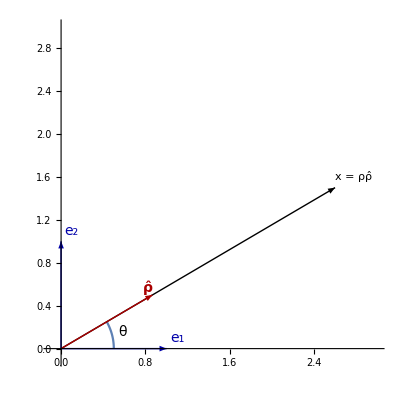

```mathematica
ClearAll[o, e1,e2, rcap, fs, bold, esub, tcap]
o = {0,0};
{e1,e2} = IdentityMatrix[2];
rcap[ t_ ] := e1 Cos[t] + e2 Sin[t];
bold := Style[#, Bold ] &;
fs := Style[#, FontSize -> 14] &;
esub := fs[Subscript["e" // bold, #]]&;
tcap := fs[bold[OverHat[#]]]  &;

p = Module[{rho,theta, x, tr},
rho = 3;
tr = 0.5;
theta = Pi/6;
x = rho rcap[theta];
Show[{
ParametricPlot[ tr rcap[t], {t, 0, theta}, PlotRange -> {{-0.1,rho}, {-0.1,rho}}, PlotStyle-> "ThickLines"],
Graphics[{
Thick,
Text["θ" //fs, 1.2 tr rcap[theta/2]],
Arrow[{o, x}],
Text[
Row[{"x" // bold//fs, " = ρ" // fs, tcap["ρ"]}], 
0.2 rcap[theta] + x ],
Blue//Darker,
Arrow[{o, e1}],
Arrow[{o, e2}],
Text[esub[1], 1.1 e1 + 0.1 e2],
Text[esub[2], 1.1 e2 + 0.1 e1],
Red//Darker,
Arrow[{o, rcap[theta]}],
Text[tcap["ρ"], rcap[1.15 theta]]
}]
}]
]
```

```mathematica
peeters`exportForLatex["curvilinearPolarFig", p]
```

{curvilinearPolarFig.eps,curvilinearPolarFigpn.png}